### Code

#### Code for sessies

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
Needs["iC`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[253518005]
```

<|Index→253518005,QCode→343233422343,RuleSet→{ABA→AAB,A→ABA}|>

We can pull out the ruleset itself:

```mathematica
rs01[["RuleSet"]]
```

{ABA→AAB,A→ABA}

Or start from a ruleset:

```mathematica
rs02=FromReducedRankRuleSet[{"AA"->"","AB"->"BA","A"->"BB","B"->"AAA"}]
```

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

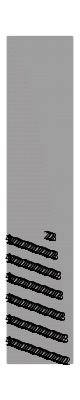


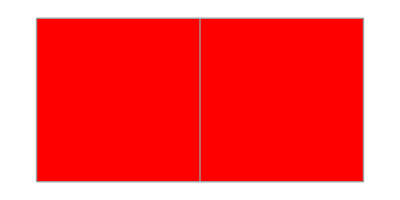

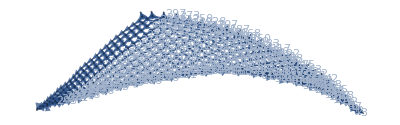
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss02=SSS[rs02, "A",400];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss02[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,«741»,398→399,373→399,399→400,373→400}

```mathematica
SSSInteractiveDisplay[sss02]
```

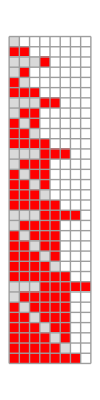
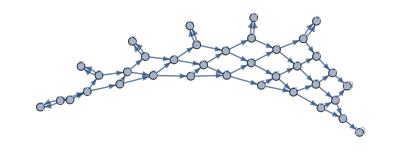
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
-Graphics--Graphics-

```mathematica
SSSDisplay[sss02,Min->1,Max->400,SSSMin->Automatic,SSSMax->32,NetMin->Automatic,NetMax->36,HighlightMethod->None,RulePlacement->Top,NetMethod->{GraphPlot},ImageSize->119.,NetSize->{Automatic,184.},SSSSize->{Automatic,269.},IconSize->{Automatic,17.05},VertexSize->0.8,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->True]
```

```mathematica
sss02[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,4→5,4→6,«736»,397→398,372→398,398→399,373→399,399→400,373→400}

```mathematica
nds02=ToNetDifferenceSets[sss02[["Net"]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,1,2},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds02,27]
```

{{373,2}}

```mathematica
nds02[[1;;373]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27}}

Try the reduction:

```mathematica
rsl02=ReduceSetList[nds02[[1;;373]]]
```

{{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},€_(n$1⊨1)^2[{1,2+n$1}],€_(n$2⊨1)^22[{3+n$2,4+n$2},{1,1,2},{},{1,3+n$2},€^(1+n$2)[{1,4+n$2}]],{26,27}}

The most compressed part is

```mathematica
rsl02[[9]]/.n$2->k
```

€_(k⊨1)^22[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

```mathematica
rsl02[[9]]//InputForm
```

```mathematica
IndexedConcatenate[{3 + k, 4 + k}, {1, 1, 2}, {}, {1, 3 + k}, 
 IndexedConcatenate[{1, 4 + k}, 1 + k], {k, -2, 22}]
```

€_(k⊨-2)^22[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

Start it earlier, stop it whenever you want:

```mathematica
IndexedConcatenate[{3 + n$2, 4 + n$2}, {1, 1, 2}, {}, {1, 3 + n$2}, IndexedConcatenate[{1, 4 + n$2}, 1 + n$2], {n$2, -2, 15}]/.n$2->k
```

€_(k⊨-2)^15[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

This is the same thing as

```mathematica
IndexedConcatenate[{n$2, n$2+1}, {1, 1, 2}, {}, {1, n$2}, IndexedConcatenate[{1, n$2+1}, n$2-2], {n$2, 1, 15}]/.n$2->k
```

€_(k⊨1)^15[{k,k+1},{1,1,2},{},{1,k},€^(k-2)[{1,k+1}]]

```mathematica
{ExpandAll[%]}
```

{{1,2},{1,1,2},{},{1,1},{2,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16}}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

-Graphics-

#### Two Linear (1D) examples

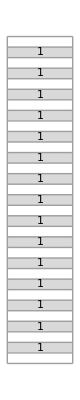
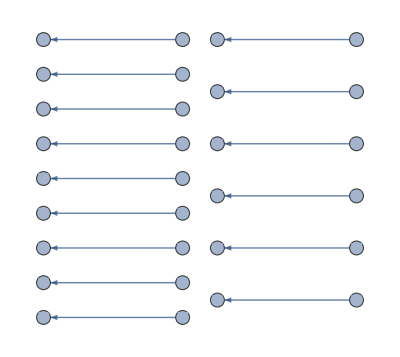
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssslin1=SSS[FromReducedRankIndex[2],"",30];
```

```mathematica
ssslin1[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30}

```mathematica
ToNetDifferenceSets[ssslin1[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1},{}],{1}}

Use most compact part:

```mathematica
{€^14[{1},{}]}
```

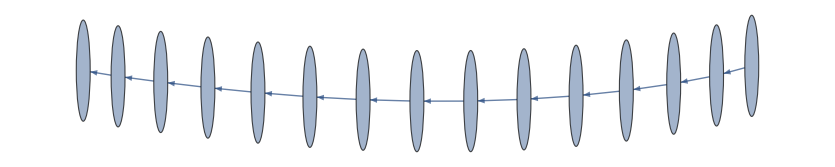
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
ssslin2=SSS[FromReducedRankIndex[4],"A",15,NetSize->550];
```

```mathematica
ssslin2[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15}

```mathematica
ToNetDifferenceSets[ssslin2[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1}]}

Note: pull up Jeanna Toulouse’s & Chris Trana’s posters, compare to their network summaries!

#### The 2D (mostly) hexagonal network

```mathematica
rsHex=FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

<|Index→1181262395,QCode→3243234232423,RuleSet→{AA→BA,AB→AA,B→AA}|>

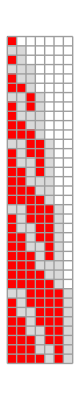
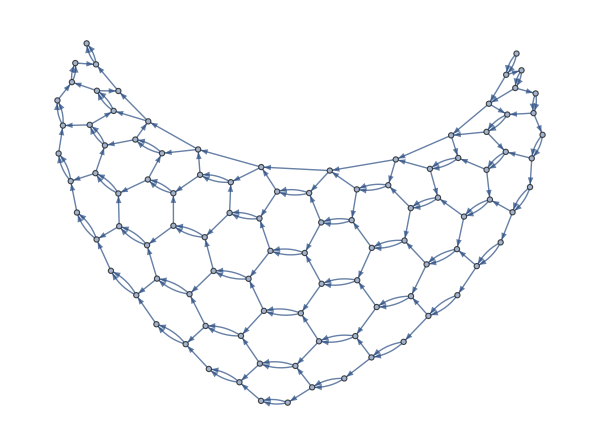
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssHex=SSS[rsHex, "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
SSSInteractiveDisplay[sssHex]
```

```mathematica
sssHex["Distance"]
```

{0,1,2,3,2,4,5,3,4,3,6,7,5,6,4,5,4,8,9,7,8,6,7,5,6,5,10,11,9,10,8,9,7,8,6,7,6,12,13,11,12,10,11,9,10,8,9,7,8,7,14,15,13,14,12,13,11,12,10,11,9,10,8,9,8,16,17,15,16,14,15,13,14,12,13,11,12,10,11,9,10,9,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,10,11,10,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,11,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,12,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,13,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,14,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,15,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,16,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,17,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,18,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,19,38,39,37,38,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21}

```mathematica
Tally[sssHex["Distance"]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,19},{21,19},{22,18},{23,17},{24,16},{25,15},{26,14},{27,13},{28,12},{29,11},{30,10},{31,9},{32,8},{33,7},{34,6},{35,5},{36,4},{37,3},{38,2},{39,1}}

```mathematica
Tally[sssHex["Distance"]][[1;;20]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19}}

```mathematica
Last/@%140
```

{1,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Accumulate[%]
```

{1,2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191}

```mathematica
NestList[Differences,%,2]//Grid
```

1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |

```mathematica
sssHex["Net"]
```

{1→2,1→2,2→3,3→4,3→4,4→5,2→5,4→6,6→7,6→7,7→8,5→8,8→9,8→9,9→10,5→10,7→11,11→12,11→12,12→13,9→13,13→14,13→14,14→15,10→15,15→16,15→16,16→17,10→17,12→18,18→19,18→19,19→20,14→20,20→21,20→21,21→22,16→22,22→23,22→23,23→24,17→24,24→25,24→25,25→26,17→26,19→27,27→28,27→28,28→29,21→29,29→30,29→30,30→31,23→31,31→32,31→32,32→33,25→33,33→34,33→34,34→35,26→35,35→36,35→36,36→37,26→37,28→38,38→39,38→39,39→40,30→40,40→41,40→41,41→42,32→42,42→43,42→43,43→44,34→44,44→45,44→45,45→46,36→46,46→47,46→47,47→48,37→48,48→49,48→49,49→50,37→50,39→51,51→52,51→52,52→53,41→53,53→54,53→54,54→55,43→55,55→56,55→56,56→57,45→57,57→58,57→58,58→59,47→59,59→60,59→60,60→61,49→61,61→62,61→62,62→63,50→63,63→64,63→64,64→65,50→65,52→66,66→67,66→67,67→68,54→68,68→69,68→69,69→70,56→70,70→71,70→71,71→72,58→72,72→73,72→73,73→74,60→74,74→75,74→75,75→76,62→76,76→77,76→77,77→78,64→78,78→79,78→79,79→80,65→80,80→81,80→81,81→82,65→82,67→83,83→84,83→84,84→85,69→85,85→86,85→86,86→87,71→87,87→88,87→88,88→89,73→89,89→90,89→90,90→91,75→91,91→92,91→92,92→93,77→93,93→94,93→94,94→95,79→95,95→96,95→96,96→97,81→97,97→98,97→98,98→99,82→99,99→100,99→100,100→101,82→101,84→102,102→103,102→103,103→104,86→104,104→105,104→105,105→106,88→106,106→107,106→107,107→108,90→108,108→109,108→109,109→110,92→110,110→111,110→111,111→112,94→112,112→113,112→113,113→114,96→114,114→115,114→115,115→116,98→116,116→117,116→117,117→118,100→118,118→119,118→119,119→120,101→120,120→121,120→121,121→122,101→122,103→123,123→124,123→124,124→125,105→125,125→126,125→126,126→127,107→127,127→128,127→128,128→129,109→129,129→130,129→130,130→131,111→131,131→132,131→132,132→133,113→133,133→134,133→134,134→135,115→135,135→136,135→136,136→137,117→137,137→138,137→138,138→139,119→139,139→140,139→140,140→141,121→141,141→142,141→142,142→143,122→143,143→144,143→144,144→145,122→145,124→146,146→147,146→147,147→148,126→148,148→149,148→149,149→150,128→150,150→151,150→151,151→152,130→152,152→153,152→153,153→154,132→154,154→155,154→155,155→156,134→156,156→157,156→157,157→158,136→158,158→159,158→159,159→160,138→160,160→161,160→161,161→162,140→162,162→163,162→163,163→164,142→164,164→165,164→165,165→166,144→166,166→167,166→167,167→168,145→168,168→169,168→169,169→170,145→170,147→171,171→172,171→172,172→173,149→173,173→174,173→174,174→175,151→175,175→176,175→176,176→177,153→177,177→178,177→178,178→179,155→179,179→180,179→180,180→181,157→181,181→182,181→182,182→183,159→183,183→184,183→184,184→185,161→185,185→186,185→186,186→187,163→187,187→188,187→188,188→189,165→189,189→190,189→190,190→191,167→191,191→192,191→192,192→193,169→193,193→194,193→194,194→195,170→195,195→196,195→196,196→197,170→197,172→198,198→199,198→199,199→200,174→200,200→201,200→201,201→202,176→202,202→203,202→203,203→204,178→204,204→205,204→205,205→206,180→206,206→207,206→207,207→208,182→208,208→209,208→209,209→210,184→210,210→211,210→211,211→212,186→212,212→213,212→213,213→214,188→214,214→215,214→215,215→216,190→216,216→217,216→217,217→218,192→218,218→219,218→219,219→220,194→220,220→221,220→221,221→222,196→222,222→223,222→223,223→224,197→224,224→225,224→225,225→226,197→226,199→227,227→228,227→228,228→229,201→229,229→230,229→230,230→231,203→231,231→232,231→232,232→233,205→233,233→234,233→234,234→235,207→235,235→236,235→236,236→237,209→237,237→238,237→238,238→239,211→239,239→240,239→240,240→241,213→241,241→242,241→242,242→243,215→243,243→244,243→244,244→245,217→245,245→246,245→246,246→247,219→247,247→248,247→248,248→249,221→249,249→250,249→250,250→251,223→251,251→252,251→252,252→253,225→253,253→254,253→254,254→255,226→255,255→256,255→256,256→257,226→257,228→258,258→259,258→259,259→260,230→260,260→261,260→261,261→262,232→262,262→263,262→263,263→264,234→264,264→265,264→265,265→266,236→266,266→267,266→267,267→268,238→268,268→269,268→269,269→270,240→270,270→271,270→271,271→272,242→272,272→273,272→273,273→274,244→274,274→275,274→275,275→276,246→276,276→277,276→277,277→278,248→278,278→279,278→279,279→280,250→280,280→281,280→281,281→282,252→282,282→283,282→283,283→284,254→284,284→285,284→285,285→286,256→286,286→287,286→287,287→288,257→288,288→289,288→289,289→290,257→290,259→291,291→292,291→292,292→293,261→293,293→294,293→294,294→295,263→295,295→296,295→296,296→297,265→297,297→298,297→298,298→299,267→299,299→300,299→300,300→301,269→301,301→302,301→302,302→303,271→303,303→304,303→304,304→305,273→305,305→306,305→306,306→307,275→307,307→308,307→308,308→309,277→309,309→310,309→310,310→311,279→311,311→312,311→312,312→313,281→313,313→314,313→314,314→315,283→315,315→316,315→316,316→317,285→317,317→318,317→318,318→319,287→319,319→320,319→320,320→321,289→321,321→322,321→322,322→323,290→323,323→324,323→324,324→325,290→325,292→326,326→327,326→327,327→328,294→328,328→329,328→329,329→330,296→330,330→331,330→331,331→332,298→332,332→333,332→333,333→334,300→334,334→335,334→335,335→336,302→336,336→337,336→337,337→338,304→338,338→339,338→339,339→340,306→340,340→341,340→341,341→342,308→342,342→343,342→343,343→344,310→344,344→345,344→345,345→346,312→346,346→347,346→347,347→348,314→348,348→349,348→349,349→350,316→350,350→351,350→351,351→352,318→352,352→353,352→353,353→354,320→354,354→355,354→355,355→356,322→356,356→357,356→357,357→358,324→358,358→359,358→359,359→360,325→360,360→361,360→361,361→362,325→362,327→363,363→364,363→364,364→365,329→365,365→366,365→366,366→367,331→367,367→368,367→368,368→369,333→369,369→370,369→370,370→371,335→371,371→372,371→372,372→373,337→373,373→374,373→374,374→375,339→375,375→376,375→376,376→377,341→377,377→378,377→378,378→379,343→379,379→380,379→380,380→381,345→381,381→382,381→382,382→383,347→383,383→384,383→384,384→385,349→385,385→386,385→386,386→387,351→387,387→388,387→388,388→389,353→389,389→390,389→390,390→391,355→391,391→392,391→392,392→393,357→393,393→394,393→394,394→395,359→395,395→396,395→396,396→397,361→397,397→398,397→398,398→399,362→399,399→400,399→400}

```mathematica
ToNetDifferenceSets[sssHex["Net"]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
ReduceSetList[%150]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{1+2 n$1,3+2 n$1},€^(1+n$1)[{1,1},{1,2 (1+n$1)}]],{37},€^18[{1,1},{1}],{1,1}}

```mathematica
Position[%,37]
```

{{325,2},{362,1}}

```mathematica
%150[[1;;362]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37}}

```mathematica
ReduceSetList[%152]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{2 n$1+1,2 n$1+3},€^(n$1+1)[{1,1},{1,2 (n$1+1)}]],{37}}

```mathematica
%153[[2]]/.n$1->k//InputForm
```

```mathematica
IndexedConcatenate[{1 + 2*k, 3 + 2*k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{1 + 2 k, 3 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2*(1 + k)}, 1 + k], {k, 0, 16}]
```

€_(k⊨0)^16[{2 k+1,2 k+3},€^(k+1)[{1,1},{1,2 (k+1)}]]

```mathematica
IndexedConcatenate[{-1 + 2 k, 1 + 2 k}, IndexedConcatenate[{1, 1}, {1, 2 k}, k], {k, 1, 17}]
```

€_(k⊨1)^17[{2 k-1,2 k+1},€^k[{1,1},{1,2 k}]]

```mathematica
{ExpandAll[%173]}=={ExpandAll[%176]}
```

True